#### code below generates PIP plot shown in Figure 2A

convave trade-off

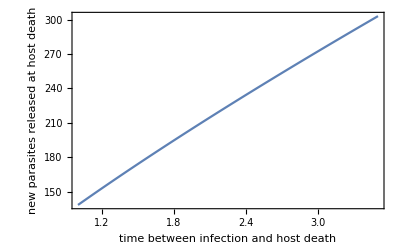

```mathematica
γxx[τx_,b_]:=b(τx+0.5)^0.8;
Plot[γxx[τ,100],{τ,1,3.5},Frame->True,FrameLabel->{Style["time between infection and host death",16,Black],Style["new parasites released\n at host death",16,Black]}]
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
vr[T_,tl_,τ_,β_,δ_,μ_, b_,s0_,0]:=vr[T,tl,τ,β,δ,μ,b,s0,0]=1;
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vr[T_,tl_,τ_,β_,δ_,μ_, b_,s0_,n_]:=
(sol=NDSolve[{
D[s[t], t]==s0 j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==vr[T,tl,τ,β,δ,μ,b,s0,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vr[T,tl,τ,β,δ,μ, b,s0,n] =First@Evaluate[v[T]/.sol])
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
vm[T_,tl_,τr_,τm_,β_,δ_,μ_, b_,s0_]:=
(sol1=NDSolve[{
D[s[t], t]==s0 j1[t,tl]-μ s[t]-s[t](β vr[t]+β vm[t]),
D[vr[t], t]== γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr]-δ vr[t]-β*s[t]*vr[t],
D[vm[t], t]== γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm]-δ vm[t]-β*s[t]*vm[t],
s[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
```

```mathematica
Clear[v0,vr0]
v0=1;
list=Table[{τrx,τmx,v0=1; vr0=vr[4,1,τrx,10^-8,1,0.25, 100,10^7,300];vm[4,1,τrx,τmx,10^-8,1,0.25,100,10^7]},{τrx,1,3.4,0.05},{τmx,1,3.4,0.05}];
```

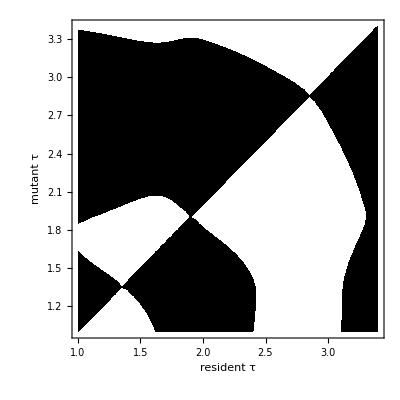

```mathematica
Flatten[list1];
list=Partition[%,3];
noto=ListContourPlot[list,PlotLabel->Style["",16,Black],FrameLabel->{Style["resident τ",20,Black],Style["mutant τ",20,Black]},LabelStyle->Directive[Bold,FontFamily->"Palatino"],ContourStyle->None,ColorFunction->(If[#1>=1,Black,White]&),ColorFunctionScaling->False,FrameTicksStyle->15,Epilog->{Rectangle[{3.3,1.85},{3.4,1}],Rectangle[{3.2,1.5},{3.4,1}],Rectangle[{3.4,2.4},{3.4,3}]}]
```

#### code below generates plots of the within-season dynamics shown in Figure 2B

```mathematica
ClearAll["Global`*"]
vrx[T_,tl_,τ_,β_,δ_,μ_, b_,s0_,0]:=vrx[T,tl,τ,β,δ,μ,b,s0,0]=1;
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vrx[T_,tl_,τ_?NumericQ,β_,δ_,μ_, b_,s0_,n_]:=
(sol=NDSolve[{
D[s[t], t]==s0 j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==vrx[T,tl,τ,β,δ,μ,b,s0,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vrx[T,tl,τ,β,δ,μ, b,s0,n] =First@Evaluate[v[T]/.sol])
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_, b_,s0_]:=
(sol1=NDSolve[{
D[s[t], t]==s0 j1[t,tl]-μ s[t]-s[t](β vr[t]+β vm[t]),
D[vr[t], t]== γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr]-δ vr[t]-β*s[t]*vr[t],
D[vm[t], t]== γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm]-δ vm[t]-β*s[t]*vm[t],
s[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]
```

transmission dynamics

```mathematica
j[t_,tl_]:=If[0<t<tl,1/tl,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
solw[tt_?NumericQ,tl_?NumericQ,τ_?NumericQ,β_,δ_,μ_, b_,s0_]:=
First@NDSolve[{D[s[t], t]==s0 j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==v0},{s,v},{t,0,tt},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
```

host incidence

```mathematica
solc[tt_?NumericQ,tl_?NumericQ,τ_?NumericQ,β_,δ_,μ_, b_,s0_]:=
First@NDSolve[{D[s[t], t]==s0 j1[t,tl]-μ s[t]-β s[t]*v[t],
D[s1[t], t]==β  *s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,s1[t/;t≤0]==0,v[t/;t≤0]==v0},{s,s1,v},{t,0,tt},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision];
```

```mathematica
essb=1.36;
v0=2.6702588961191285*^8;
xb=Plot[{Evaluate[v[t]/.solw[4,1,essb,10^-8,1,0.25, 100,10^7]]},{t,0,4},Evaluated->True,PlotRange->{{0,4},{0,7*10^8}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{LightGray,Thickness[0.01]}},AxesStyle->Opacity[0],Axes->False,Frame->True,(*FrameTicksStyle->Opacity[0],*)(*FrameTicks->{{None,None},{{#,#,{0.03,0}}&/@ticks,None}},*)FrameStyle->Thick(*Epilog->{Style[Text["i",{3.1,2100000000}],25,Italic,FontFamily->"Times"],Style[Text["ii",{3.1,800000000}],25,Italic,FontFamily->"Times"]}*)];
```

```mathematica
vr[4,1,1.36,10^-8,1,0.25, 100,10^7,100]
```

2.67026×10^8

```mathematica
essb=1.36;
v0=2.6702588961191285*^8;
yy2=Plot[{D[s1[t]/.solc[4,1,essb,10^-8,1,0.25, 100,10^7],t]/.t->u/.t->u},{u,0,4},Evaluated->True,PlotRange->{{0,4},{0,10000000}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{Black,Thickness[0.01]},{Thickness[0.01],Dashing[Medium],Darker[Blue]}},Frame->True,FrameStyle->Thick];
```

```mathematica
zz1=Labeled[Overlay[{xb,yy2}],{Style["time",FontFamily->"Helvetica",FontSize->22],Rotate[Style["
",FontFamily->"Helvetica",FontSize->22],180 Degree],Style["polycyclic attractor",FontFamily->"Helvetica",FontSize->28], Style["    host and parasite\n          dynamics",FontFamily->"Helvetica",FontSize->28]},{Bottom,Right,Top,Left},RotateLabel->True];
```

```mathematica
essa=2.85;
v0=5.570697462270721*^8;
xxa=Plot[{Evaluate[v[t]/.solw[4,1,essa,10^-8,1,0.25, 100,10^7]]},{t,0,4},Evaluated->True,PlotRange->{{0,4},{0,7*10^8}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{Gray,Thickness[0.01]}},AxesStyle->Opacity[0],Axes->False,Frame->True,(*FrameTicksStyle->Opacity[0],*)(*FrameTicks->{{None,None},{{#,#,{0.03,0}}&/@ticks,None}},*)FrameStyle->Thick(*Epilog->{Style[Text["i",{3.1,2100000000}],25,Italic,FontFamily->"Times"],Style[Text["ii",{3.1,800000000}],25,Italic,FontFamily->"Times"]}*)];
```

```mathematica
essa=2.85;
v0=5.570697462270721*^8;
yy2=Plot[{D[s1[t]/.solc[4,1,essa,10^-8,1,0.25, 100,10^7],t]/.t->u/.t->u},{u,0,4},Evaluated->True,PlotRange->{{0,4},{0,10000000}},FrameTicks->{{None,None},{{0,1,2,3,4},None}},FrameTicksStyle->20,PlotStyle->{{Black,Thickness[0.01]},{Thickness[0.01],Dashing[Medium],Darker[Blue]}},Frame->True,FrameStyle->Thick];
```

```mathematica
zz2=Labeled[Overlay[{xxa,yy2}],{Style["time\n \n",FontFamily->"Helvetica",FontSize->22],Rotate[Style["
",FontFamily->"Helvetica",FontSize->22],180 Degree],Style["monocyclic attractor",FontFamily->"Helvetica",FontSize->28], Style["    host and parasite\n          dynamics",FontFamily->"Helvetica",FontSize->28]},{Bottom,Right,Top,Left},RotateLabel->True];
```

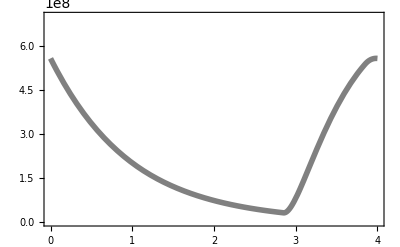
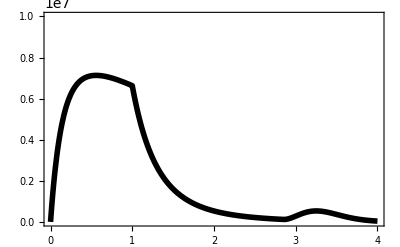
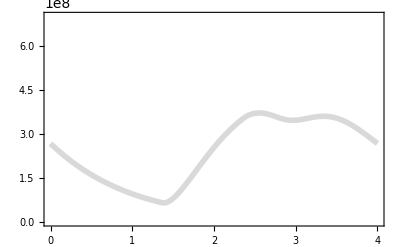
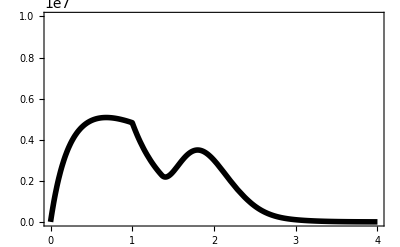
-Graphics--Graphics-time
 

monocyclic attractor    host and parasite
          dynamics
-Graphics--Graphics-time
polycyclic attractor    host and parasite
          dynamics

```mathematica
n3=Style[Grid[{{zz2},{zz1}},Spacings->0],ImageSizeMultipliers->{1,1}]
```

#### code below generates plots in Figure 4

*** max virulence is τ = 1 ***

```mathematica
ClearAll["Global`*"]
vrx[T_,tl_,τ_,β_,δ_,μ_, b_,s0_,0]:=vrx[T,tl,τ,β,δ,μ,b,s0,0]=1;
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
(*vrx[] outputs the density of parasites at t = T in season n*)
vrx[T_,tl_,τ_?NumericQ,β_,δ_,μ_, b_,s0_,n_]:=
(sol=NDSolve[{
D[s[t], t]==s0 j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==vrx[T,tl,τ,β,δ,μ,b,s0,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vrx[T,tl,τ,β,δ,μ, b,s0,n] =First@Evaluate[v[T]/.sol])
(*vmx[] outputs the density of mutant parasites at t = T in the season the mutant is introduced*)
vmx[T_,tl_,τr_?NumericQ,τm_?NumericQ,β_,δ_,μ_, b_,s0_]:=
(sol1=NDSolve[{
D[s[t], t]==s0 j1[t,tl]-μ s[t]-s[t](β vr[t]+β vm[t]),
D[vr[t], t]== γxx[τr,b] β Exp[-τr μ]*s[t-τr]*vr[t-τr]-δ vr[t]-β*s[t]*vr[t],
D[vm[t], t]== γxx[τm,b] β Exp[-τm μ]*s[t-τm]*vm[t-τm]-δ vm[t]-β*s[t]*vm[t],
s[t/;t≤0]==0,vr[t/;t≤0]==vr0,vm[t/;t≤0]==1}, 
{vm},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
First@Evaluate[vm[T]/.sol1])
Needs["NumericalCalculus`"]

(*code below finds high virulence ess, low virulence ess and repellor in between the two ess points*)
essfunc[listx_,ttx_,tlx_,tx_,β_,δ_,μ_,b_,s0_]:=(
alist=Select[listx,#[[2]]>0&];(*select ess points*)
(*check if τ = 1 (max virulence) is an attractor*)
(vr0=vrx[ttx,tlx,1,β,δ,μ, b,s0,300];
a=vmx[ttx,tlx,1,1+0.01,β,δ,μ, b,s0];If[a<1,ylist=Join[{{1,1}},alist]]);
If[Length@ylist>2,xlist={#1,#3}&@@ylist, xlist=ylist];
yy={#1}&@@@xlist;(*grab ess values*)
zz=Flatten@yy;
(*if there is >1 ess, find the repellor by finding the minimum between the two ess points *)
If[Length[zz]>1,{minlist=Table[{τx,v0=1; vr0=vrx[ttx,tlx,τx,β,δ,μ, b,s0,300];
ND[vmx[ttx,tlx,τrx,τrx,β,δ,μ, b,s0],τrx,τx]},{τx,First@zz,Last@zz,0.005}];
rep=Flatten@Partition[minlist,2,1];
repc=Partition[rep,4];
(*sign change is where repellor is located*)
repp=Select[repc,Sign[#[[2]]]<Sign[#[[4]]]&];
(*grab values of τ before and after sign change*)
repx={#1,#3}&@@@repp;
(*take mean of values of τ before and after sign change*)
bb=Mean/@repx;
(*join and sort two ess points and repellor*)
yy=Sort[Join[bb,zz]]},yy=zz];
q=Table[tx,{Length[yy]}];
(*add value of tl or T to ess points and repellor*)
xm1=Transpose[{q,yy}];
(*if there is more than one repellor,find the global max by determining which ess competitively excludes the other ess, assign 1 to global max, 2 to repellor and 3 to local max*)
If[Length[zz]>1,{inv=(v0=1; vr0=vrx[ttx,tlx,zz[[1]],β,δ,μ, b,s0,50];vmx[ttx,tlx,zz[[1]],zz[[2]],β,δ,μ, b,s0]),If[inv<1,h={1,2,3},h={3,2,1}]},h={1}];
listf=Partition[Flatten@Transpose[{xm1,h}],Length[yy]])
```

```mathematica
tlx=0.25;
list0=Table[{τx,v0=1; 
(*resident eq density*)
vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,50];
(*mutant density w/ τm = τr + 0.01 at t = T*)
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
(*mutant density w/ τm = τr - 0.01 at t = T*)
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
(*if both the fitness of both mutants is <1, τr is an ess, assign 1 to this value of τ, otherwise assign it 0 to denote that it is not an ess*)
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3.6,0.01}]
```

```mathematica
tlx=0.25;
listtlx00=essfunc[list0,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{0.25,1.29,3},{0.25,1.9375,2},{0.25,3.53,1}}

```mathematica
tlx=0.5;
list1=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,50];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3.4,0.01}];
```

```mathematica
tlx=0.5;
listtlx1=essfunc[list1,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{0.5,1.36,3},{0.5,1.915,2},{0.5,3.31,1}}

```mathematica
tlx=0.75;
list2=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,50];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3.1,0.01}];
```

```mathematica
tlx=0.75;
listtlx2=essfunc[list2,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{0.75,1.38,3},{0.75,1.915,2},{0.75,3.08,1}}

```mathematica
tlx=1;
list3=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,50];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
tlx=1;
listtlx3=essfunc[list3,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{1,1.36,3},{1,1.905,2},{1,2.85,1}}

```mathematica
tlx=1.25;
list4=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,50];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
tlx=1.25;
listtlx4=essfunc[list4,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{1.25,1.33,3},{1.25,1.915,2},{1.25,2.64,1}}

```mathematica
tlx=1.5;
list5=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,50];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
tlx=1.5;
listtlx5=essfunc[list5,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{1.5,1.3,3},{1.5,1.925,2},{1.5,2.44,1}}

```mathematica
tlx=1.75;
list6=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
tlx=1.75;
listtlx6=essfunc[list6,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{1.75,1.31,1},{1.75,1.935,2},{1.75,2.3,3}}

```mathematica
tlx=2;
list7=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
tlx=2;
listtlx7=essfunc[list7,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{2,1.32,1},{2,1.965,2},{2,2.3,3}}

```mathematica
tlx=2.25;
list8=ParallelTable[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,200];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.9,0.01}]
```

```mathematica
tlx=2.25;
listtlx8=essfunc[list8,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{2.25,1.3,1},{2.25,1.965,2},{2.25,2.3,3}}

```mathematica
tlx=2.5;
list9=Table[{τx,v0=1; vr0=vrx[4,tlx,τx,10^-8,1,0.25, 100,10^7,300];
x=vmx[4,tlx,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[4,tlx,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.5,0.01}]
```

```mathematica
tlx=2.5;
listtlx9=essfunc[list9,4,tlx,tlx,10^-8,1,0.25, 100,10^7]
```

{{2.5,1.02,1},{2.5,1.965,2},{2.5,2.29,3}}

```mathematica
listall=Join[listtlx0,listtlx1,listtlx2,listtlx3,listtlx4,listtlx5,listtlx6,listtlx7,listtlx8,listtlx9];
```

```mathematica
max=Select[listall,#[[3]]==1&];
rep=Select[listall,#[[3]]==2&];
min=Select[listall,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

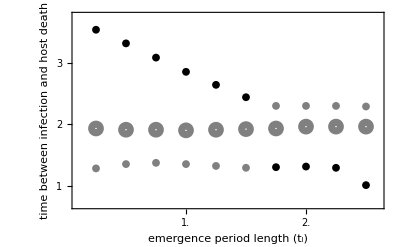

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,4.5,0.5],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0.1,2.6},{0.7,3.75}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["time between infection\n and host death",16,FontFamily->"Helvetica"],None},{Style["emergence period length (t_l)",16,FontFamily->"Helvetica"],None}}]
```

```mathematica
ttx=2.75;
list0=Table[{τx,v0=1; vr0=vrx[ttx,1,τx,10^-8,1,0.25, 100,10^7,300];
x=vmx[ttx,1,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[ttx,1,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2,0.005}];
```

```mathematica
ttx=2.75;
listttx00=essfunc[list0,ttx,1,ttx,10^-8,1,0.25, 100,10^7]
```

{{2.75,1,3},{2.75,1.2525,2},{2.75,1.645,1}}

```mathematica
ttx=3;
list1=Table[{τx,v0=1; vr0=vrx[ttx,1,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[ttx,1,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[ttx,1,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.005}];
```

```mathematica
ttx=3;
listttx0=essfunc[list1,ttx,1,ttx,10^-8,1,0.25, 100,10^7]
```

{{3,1.045,3},{3,1.45,2},{3,1.885,1}}

```mathematica
ttx=3.25;
list2=ParallelTable[{τx,v0=1; vr0=vrx[ttx,1,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[ttx,1,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[ttx,1,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.2,0.0025}]
```

```mathematica
ttx=3.25;
listttx1=essfunc[list2,ttx,1,ttx,10^-8,1,0.25, 100,10^7]
```

{{3.25,1.1225,3},{3.25,1.5175,2},{3.25,2.1225,1}}

```mathematica
ttx=3.5;
list3=ParallelTable[{τx,v0=1; vr0=vrx[ttx,1,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[ttx,1,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[ttx,1,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.5,0.005}];
```

```mathematica
ttx=3.5;
listttx2=essfunc[list3,ttx,1,ttx,10^-8,1,0.25, 100,10^7]
```

{{3.5,1.2,3},{3.5,1.635,2},{3.5,2.365,1}}

```mathematica
ttx=3.75;
list4=ParallelTable[{τx,v0=1; vr0=vrx[ttx,1,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[ttx,1,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[ttx,1,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.8,0.01}];
```

```mathematica
ttx=3.75;
listttx3=essfunc[list4,ttx,1,ttx,10^-8,1,0.25, 100,10^7]
```

{{3.75,1.28,3},{3.75,1.765,2},{3.75,2.61,1}}

```mathematica
ttx=4;
list=ParallelTable[{τx,v0=1; vr0=vrx[ttx,1,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[ttx,1,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[ttx,1,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
ttx=4;
listttx4=essfunc[list5,ttx,1,ttx,10^-8,1,0.25, 100,10^7]
```

{{4,1.36,3},{4,1.895,2},{4,2.85,1}}

```mathematica
ttx=4.25;
list=ParallelTable[{τx,v0=1; vr0=vrx[ttx,1,τx,10^-8,1,0.25, 100,10^7,100];
x=vmx[ttx,1,τx,τx+0.01,10^-8,1,0.25, 100,10^7];
y=vmx[ttx,1,τx,τx-0.01,10^-8,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3.2,0.01}];
```

```mathematica
ttx=4.25;
listttx5=essfunc[list6,ttx,1,ttx,10^-8,1,0.25, 100,10^7]
```

{{4.25,1.43,3},{4.25,2.035,2},{4.25,3.1,1}}

```mathematica
all=Join[listttx00,listttx0,listttx1,listttx2,listttx3,listttx4,listttx5];
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

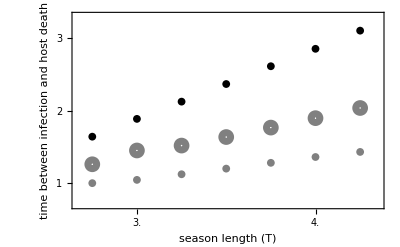

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[2,4.5,0.5],None}};
lptt=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{2.67,4.35},{0.7,3.3}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["time between infection\n and host death",16,FontFamily->"Helvetica"],None},{Style["season length (T)",16,FontFamily->"Helvetica"],None}}]
```

#### code below generates plots in Figure 5

```mathematica
μx=0;
list0=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,μx, 100,10^7,100];
x=vmx[4,1,τx,τx+0.01,10^-8,1,μx, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,μx, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
μx=0;
listmux0=essfunc[list0,4,1,μx,10^-8,1,μx, 100,10^7]
```

{0,2.96,1}

```mathematica
μx=0.1;
list1=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,μx, 100,10^7,100];
x=vmx[4,1,τx,τx+0.01,10^-8,1,μx, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,μx, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
μx=0.1;
listmux1=essfunc[list1,4,1,μx,10^-8,1,μx, 100,10^7]
```

{{0.1,1.56,3},{0.1,1.955,2},{0.1,2.93,1}}

```mathematica
μx=0.2;
list2=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,μx, 100,10^7,100];
x=vmx[4,1,τx,τx+0.01,10^-8,1,μx, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,μx, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
μx=0.2;
listmux2=essfunc[list2,4,1,μx,10^-8,1,μx, 100,10^7]
```

{{0.2,1.42,3},{0.2,1.905,2},{0.2,2.89,1}}

```mathematica
μx=0.3;
list3=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,μx, 100,10^7,100];
x=vmx[4,1,τx,τx+0.01,10^-8,1,μx, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,μx, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
μx=0.3;
listmux3=essfunc[list3,4,1,μx,10^-8,1,μx, 100,10^7]
```

{{0.3,1.3,3},{0.3,1.885,2},{0.3,2.81,1}}

```mathematica
μx=0.4;
list4=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,μx, 100,10^7,100];
x=vmx[4,1,τx,τx+0.01,10^-8,1,μx, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,μx, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
μx=0.4;
listmux4=essfunc[list4,4,1,μx,10^-8,1,μx, 100,10^7]
```

{{0.4,1,3},{0.4,1.915,2},{0.4,2.71,1}}

```mathematica
μx=0.5;
list5=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,μx, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,1,μx, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,μx, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.9,0.005}];
```

```mathematica
μx=0.5;
listmux5=essfunc[list5,4,1,μx,10^-8,1,μx, 100,10^7]
```

{{0.5,1,1},{0.5,1.915,2},{0.5,2.56,3}}

```mathematica
μx=0.6;
list6=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,μx, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,1,μx, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,μx, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.9,0.005}];
```

```mathematica
μx=0.6;
listmux6=Flatten@essfunc[list6,4,1,μx,10^-8,1,μx, 100,10^7]
```

{0.6,1,1}

```mathematica
all=Join[listmux0,listmux1,listmux2,listmux3,listmux4,listmux5,listmux6];
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

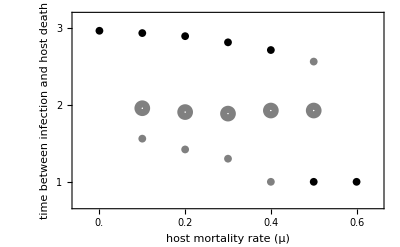

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0,0.6,0.2],None}};
lpmu=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{-.05,0.65},{0.7,3.15}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["time between infection\n and host death",16,FontFamily->"Helvetica"],None},{Style["host mortality rate (μ)",16,FontFamily->"Helvetica"],None}}]
```

```mathematica
δx=0.25;
list0=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,δx,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,δx,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,δx,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,0.5,2.9,0.005}];
```

```mathematica
δx=0.25;
listdeltax0=essfunc[list0,4,1,δx,10^-8,δx,0.25, 100,10^7]
```

{0.25,2.88,1}

```mathematica
δx=0.5;
list1=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,δx,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,δx,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,δx,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
δx=0.5;
listdeltax1=essfunc[list1,4,1,δx,10^-8,δx,0.25, 100,10^7]
```

{0.5,2.86,1}

```mathematica
δx=0.75;
list=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,δx,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,δx,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,δx,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
δx=0.75;
listdeltax2=essfunc[list2,4,1,δx,10^-8,δx,0.25, 100,10^7]
```

{0.75,2.85,1}

```mathematica
δx=1;
list3=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,δx,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,δx,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,δx,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
δx=1;
listdeltax3=essfunc[list3,4,1,δx,10^-8,δx,0.25, 100,10^7]
```

{{1,1.36,3},{1,1.935,2},{1,2.85,1}}

```mathematica
δx=1.25;
list4=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,δx,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,δx,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,δx,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
δx=1.25;
listdeltax4=essfunc[list4,4,1,δx,10^-8,δx,0.25, 100,10^7]
```

{{1.25,1.35,3},{1.25,1.935,2},{1.25,2.88,1}}

```mathematica
all=Join[listdeltax0,listdeltax1,listdeltax2,listdeltax3,listdeltax4];
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

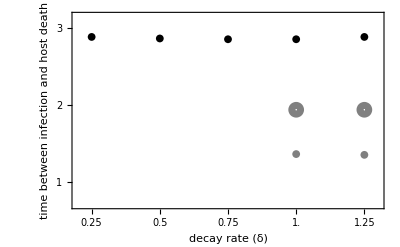

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[0.25,1.25,0.25],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{0.2,1.3},{0.7,3.15}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["time between infection\n and host death",16,FontFamily->"Helvetica"],None},{Style["decay rate (δ)",16,FontFamily->"Helvetica"],None}}]
```

```mathematica
βx=4*10^-9;
list0=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,βx,1,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,βx,1,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,βx,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,2.5,0.01}];
```

```mathematica
βx=4*10^-9;
listbeta0=Flatten@essfunc[list0,4,1,βx,βx,1,0.25, 100,10^7]
```

{{1/250000000,1,1}}

```mathematica
βx=5*10^-9;
list1=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,βx,1,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,βx,1,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,βx,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
βx=5*10^-9;
listbeta1=essfunc[list1,4,1,βx,βx,1,0.25, 100,10^7]
```

{{1/200000000,1,3},{1/200000000,1.905,2},{1/200000000,2.7,1}}

```mathematica
βx=8*10^-9;
list2=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,βx,1,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,βx,1,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,βx,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
βx=8*10^-9;
listbeta2=essfunc[list2,4,1,βx,βx,1,0.25, 100,10^7]
```

{{1/125000000,1.33,3},{1/125000000,1.915,2},{1/125000000,2.82,1}}

```mathematica
βx=10^-8;
list3=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,βx,1,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,βx,1,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,βx,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
βx=8*10^-9;
listbeta3=essfunc[list3,4,1,βx,βx,1,0.25, 100,10^7]
```

{{1/100000000,1.36,3},{1/100000000,1.905,2},{1/100000000,2.85,1}}

```mathematica
βx=1.5*10^-8;
list4=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,βx,1,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,βx,1,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,βx,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
βx=1.5*10^-8;
listbeta4=essfunc[list4,4,1,βx,βx,1,0.25, 100,10^7]
```

{{1.5×10^-8,1,3},{1.5×10^-8,1.885,2},{1.5×10^-8,2.9,1}}

```mathematica
βx=2*10^-8;
list5=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,βx,1,0.25, 100,10^7,300];
x=vmx[4,1,τx,τx+0.01,βx,1,0.25, 100,10^7];
y=vmx[4,1,τx,τx-0.01,βx,1,0.25, 100,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
βx=2*10^-8;
listbeta5=essfunc[list5,4,1,βx,βx,1,0.25, 100,10^7]
```

{{1/50000000,1,3},{1/50000000,1.935,2},{1/50000000,2.93,1}}

```mathematica
all=Join[listbeta0,listbeta1,listbeta2,listbeta3,listbeta4,listbeta5];
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

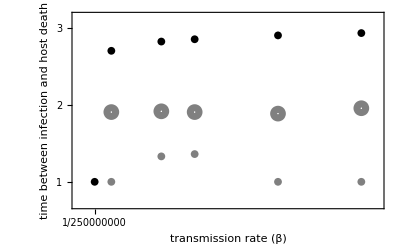

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[1/250000000,1/10000000,1/100000000],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{3*10^-9,2.1*10^-8},{0.7,3.15}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["time between infection\n and host death",16,FontFamily->"Helvetica"],None},{Style["transmission rate (β)",16,FontFamily->"Helvetica"],None}}]
```

```mathematica
bx=50;
list0=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,0.25, bx,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,1,0.25, bx,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,0.25, bx,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,1.5,0.01}];
```

```mathematica
bx=50;
listbx0=essfunc[list0,4,1,bx,10^-8,1,0.25, bx,10^7]
```

{{50,0.92,1}}

```mathematica
bx=100;
list1=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,0.25, bx,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,1,0.25, bx,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,0.25, bx,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
bx=100;
listbx1=essfunc[list1,4,1,bx,10^-8,1,0.25, bx,10^7]
```

{{100,1.36,3},{100,1.935,2},{100,2.85,1}}

```mathematica
bx=150;
list2=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,0.25, bx,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,1,0.25, bx,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,0.25, bx,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
bx=150;
listbx2=essfunc[list2,4,1,bx,10^-8,1,0.25, bx,10^7]
```

{{150,1.44,3},{150,1.925,2},{150,2.9,1}}

```mathematica
bx=200;
list3=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,0.25, bx,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,1,0.25, bx,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,0.25, bx,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
bx=200;
listbx3=essfunc[list3,4,1,bx,10^-8,1,0.25, bx,10^7]
```

{200,2.93,1}

```mathematica
bx=250;
list4=ParallelTable[{τx,v0=1; vr0=vrx[4,1,τx,10^-8,1,0.25, bx,10^7,300];
x=vmx[4,1,τx,τx+0.01,10^-8,1,0.25, bx,10^7];
y=vmx[4,1,τx,τx-0.01,10^-8,1,0.25, bx,10^7];
If[x<1&&y<1,τxx=1,τxx=0]},{τx,1,3,0.01}];
```

```mathematica
bx=250;
listbx4=essfunc[list4,4,1,bx,10^-8,1,0.25, bx,10^7]
```

{250,2.94,1}

```mathematica
all=Join[listbx0,listbx1,listbx2,listbx3,listbx4];
max=Select[all,#[[3]]==1&];
rep=Select[all,#[[3]]==2&];
min=Select[all,#[[3]]==3&];
maxx={#1,#2}&@@@max;
mix={#1,#2}&@@@min;
repx={#1,#2}&@@@rep;
```

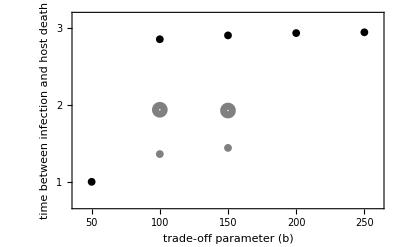

```mathematica
ftrange={{{#,#,{0.03,0}}&/@Range[1,3,1],None},{{#,#,{0.03,0}}&/@Range[50,250,50],None}};
lptl=ListPlot[{maxx,mix,repx},Frame->{{True,True},{True,True}},PlotRange->{{40,260},{0.7,3.15}},PlotStyle->{{Automatic,Black,AbsoluteThickness[10]},{Automatic,Gray,AbsoluteThickness[10]},{Gray,AbsoluteThickness[10]}},FrameTicks->ftrange,FrameStyle->Directive[Black,Thick],PlotMarkers->{Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Disk[]},ImageSize->8],Graphics[{Thick,Circle[]},ImageSize->9]},FrameTicksStyle->{{14,FontFamily->"Helvetica"},{14,FontFamily->"Helvetica"}},FrameLabel->{{Style["time between infection\n and host death",16,FontFamily->"Helvetica"],None},{Style["trade-off parameter (b)",16,FontFamily->"Helvetica"],None}}]
```

#### code below generates bifurcation plot shown in Figure 6A

```mathematica
ClearAll["Global`*"]
```

```mathematica
vcr[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,0]:=vcr[T,tl,τ,β,δ,μ,b,σ,ρ,0]=1;
j1[t_,tlx_]:=If[0<t<tlx,1/tlx,0];
γxx[τx_,b_]:=b(τx+0.5)^0.8;
vcr[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]* j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]}, 
{v},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
vcr[T,tl,τ,β,δ,μ, b,σ,ρ,n] =First@Evaluate[v[T]/.sol])
sc[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,0]:=sc[T,tl,τ,β,δ,μ,b,σ,ρ,0]=10^7;
sc[T_,tl_,τ_,β_,δ_,μ_, b_,σ_,ρ_,n_]:=
(sol=NDSolve[{
D[s[t], t]==sc[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]* j1[t,tl]-μ s[t]-β s[t]*v[t],
D[v[t], t]==γxx[τ,b] β Exp[-τ μ]*s[t-τ]*v[t-τ] -δ v[t]-β s[t]*v[t],
s[t/;t≤0]==0,v[t/;t≤0]==vcr[T,tl,τ,β,δ,μ,b,σ,ρ,n-1]}, 
{s},{t,0,T},MaxStepSize->10^1000,MaxSteps->10^6,WorkingPrecision->MachinePrecision,Method->{"StiffnessSwitching"}];
sc[T,tl,τ,β,δ,μ, b,σ,ρ,n]=First@Evaluate[(σ s[T]/(1+ρ s[T]))/.sol])
```

```mathematica
Clear[v10,s0];
v0=1;s0=10^7;
all=Flatten[ParallelTable[seq=vcr[4,1,τx,10^-7,1,0.25,75, 200,0.0001,#]&/@Range[1000];
seq1000=Union[seq[[900;;1000]]];
Thread[{ConstantArray[τx,Length[seq1000]],seq1000}],{τx,1,3.1,0.01}],1];
```

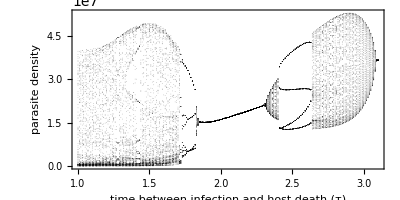

```mathematica
Graphics[{PointSize[0.001],Opacity[0.4],Point[all]},AspectRatio->1/2,Frame->True,FrameStyle->14,FrameLabel->{"time between infection and host death (τ)","parasite density",""}]
```